```mathematica
SetDirectory[NotebookDirectory[]]
c0=0;
c1=p/1200;
c3=1.0 p/(200+p);
fa=(1-c)^(1/betaA);
fe=(1-c)^betaT;
sstar=d/(a fa);
bstar=(p-ksat sstar^gamma)/(e0 fe sstar);
sub={betaA->1,betaT->1.1,d->0.01,a->0.05,ksat->800,gamma->10,e0->5};
```

/Users/yairmau/Library/CloudStorage/GoogleDrive-yair.mau@mail.huji.ac.il/.shortcut-targets-by-id/11zq27bNZ5w2XXe3YZAbbBVeoszVZY8Dq/SGH-paper/make_figures/tree_cover_mechanism

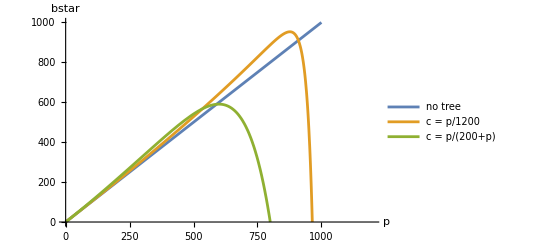

graph2.pdf

```mathematica
graph1=Plot[
{
bstar/.sub/.c->c0,
bstar/.sub/.c->c1,
bstar/.sub/.c->c3
},{p,0,1200},
AxesLabel->{"p","bstar"},
PlotRange->{{0,1200},{0,1000}},
(*PlotRange->Full,*)
PlotLegends->{"no tree","c = p/1200","c = p/(200+p)"}
]
Export["graph2.pdf",graph1]
```